```mathematica
Clear["Global`*"];
```

```mathematica
pers1:=(2G m'[r])/r^2==8π G ρ[p[r]]+(l/r)^2((1-(2G m[r])/r)c''[r]/c[r]-c'[r]/c[r] D[(G m[r])/r,r]-3/4(1-(2G m[r])/r)(c'[r]/c[r])^2)
```

```mathematica
pers2:=c'[r]/(r c[r])-(2G m[r])/(r^2(r-2G m[r]))==(8π G p[r])/(1-2G m[r]/r)-l^2/4(c'[r]/(r c[r]))^2
```

```mathematica
pers3:=p'[r]==-1/2(ρ[p[r]]+p[r])c'[r]/c[r]
```

```mathematica
definisiλ:=λ==√(1+(2 G l^2 (m[r]+4 π r^3 p[r]))/(r^2(r-2 G m[r])))
```

```mathematica
akar1λ:=c'[r]->-c[r]/l^2 2r (1 +λ)
```

```mathematica
D[akar1λ,r]//Simplify
```

c''[r]→-(2 (1+λ) (c[r]+r c'[r]))/l^2

```mathematica
pers1/.{D[akar1λ,r]}/.{akar1λ}//Expand
```

(2 G m'[r])/r^2==1/l^2-2/r^2+(2 λ)/l^2-(2 λ)/r^2+λ^2/l^2+(2 G m[r])/r^3-(2 G m[r])/(l^2 r)+(2 G λ m[r])/r^3-(4 G λ m[r])/(l^2 r)-(2 G λ^2 m[r])/(l^2 r)+8 G π ρ[p[r]]+(2 G m'[r])/r^2+(2 G λ m'[r])/r^2

```mathematica
persbaru=pers1/.{D[akar1λ,r]}/.{akar1λ}//Expand
```

(2 G m'[r])/r^2==1/l^2-2/r^2+(2 λ)/l^2-(2 λ)/r^2+λ^2/l^2+(2 G m[r])/r^3-(2 G m[r])/(l^2 r)+(2 G λ m[r])/r^3-(4 G λ m[r])/(l^2 r)-(2 G λ^2 m[r])/(l^2 r)+8 G π ρ[p[r]]+(2 G m'[r])/r^2+(2 G λ m'[r])/r^2

```mathematica
definisim=(Solve[definisiλ,m[r]]//Simplify)[[1,1]]
```

m[r]→(r^3 (-1+λ^2-8 G l^2 π p[r]))/(2 G (l^2+r^2 (-1+λ^2)))

```mathematica
D[definisim,r]
```

m'[r]→-(r^4 (-1+λ^2) (-1+λ^2-8 G l^2 π p[r]))/(G (l^2+r^2 (-1+λ^2))^2)+(3 r^2 (-1+λ^2-8 G l^2 π p[r]))/(2 G (l^2+r^2 (-1+λ^2)))-(4 l^2 π r^3 p'[r])/(l^2+r^2 (-1+λ^2))

```mathematica
persbaru1=persbaru/.{D[definisim,r]}/.{definisim}//Simplify
```

1/(r (l^2+r^2 (-1+λ^2)))(l^4-2 l^2 r^2+r^4+l^4 λ-l^2 r^2 λ+r^4 λ+l^2 r^2 λ^2-r^4 λ^2-r^4 λ^3+4 G π r^2 (-r^4 (-1+λ) (1+λ)^3+l^4 (1+4 λ)+2 l^2 r^2 (-1-2 λ+λ^3)) p[r]-4 G π r^2 (l^2+r^2 (-1+λ^2))^2 ρ[p[r]]+4 G l^4 π r^3 λ p'[r]-4 G l^2 π r^5 λ p'[r]+4 G l^2 π r^5 λ^3 p'[r])==0

```mathematica
definisiρ=(Solve[pers3/.{akar1λ},ρ[p[r]]]//Simplify)[[1,1]]
```

ρ[p[r]]→(-r (1+λ) p[r]+l^2 p'[r])/(r (1+λ))

```mathematica
Solve[persbaru1/.{definisiρ},p'[r]]//Simplify
```

{{p'[r]→((1+λ) (l^4 (1+λ)-r^4 (-1+λ) (1+λ)^2+l^2 r^2 (-2-λ+λ^2)+8 G π r^2 (-r^4 (-1+λ) (1+λ)^2+l^4 (1+2 λ)+l^2 r^2 (-2-2 λ+λ^2+λ^3)) p[r]))/(4 G l^2 π r (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))}}

```mathematica
Series[((1+λ) (l^4 (1+λ)-r^4 (-1+λ) (1+λ)^2+l^2 r^2 (-2-λ+λ^2)+8 G π r^2 (-r^4 (-1+λ) (1+λ)^2+l^4 (1+2 λ)+l^2 r^2 (-2-2 λ+λ^2+λ^3)) p[r]))/(4 G l^2 π r (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2))),{p[r],0,1}]//Simplify
```

((1+λ)^2 (l^4+l^2 r^2 (-2+λ)-r^4 (-1+λ^2)))/(4 G l^2 π r (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))+(2 r (1+λ) (-r^4 (-1+λ) (1+λ)^2+l^4 (1+2 λ)+l^2 r^2 (-2-2 λ+λ^2+λ^3)) p[r])/(l^2 (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))+O[p[r]]^2

Catatan:
λ=10000.0;
l=9.5* 10.^3;(*√(10/(12π)) 1.616 10^-35;*)
r0=11.7*10.^3;rn=10.^-6;
p0=-10.^-9; hasilnya rc=95.

Catatan:
λ=10.0;
l=3.* 10.^0;(*√(10/(12π)) 1.616 10^-35;*)
r0=10.*10.^3;rn=10.^-6;
p0=-10.^-9;hasilnya rc=0.905

```mathematica
Clear["Global`*"];

persp:=p'[r]==((1+λ)^2 (l^4+l^2 r^2 (-2+λ)-r^4 (-1+λ^2)))/(4 G l^2 π r (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))+(2 r (1+λ) (-r^4 (-1+λ) (1+λ)^2+l^4 (1+2 λ)+l^2 r^2 (-2-2 λ+λ^2+λ^3)) p[r])/(l^2 (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))

G=1.323790281083862 10^-12;
ms=1.1154605324408694 10^15;
λ=10.0;
l=3.* 10.^0;(*√(10/(12π)) 1.616 10^-35;*)
r0=10.*10.^3;rn=10.^-6;
p0=-10.^-9;
```

```mathematica
s=NDSolve[{persp,p[r0]==p0,WhenEvent[r==0,{rbs=r,"StopIntegration"}]},{p},{r,r0,rn}]
rbs
```

{{p→InterpolatingFunction[{{0.904534, 10000.}}, <>]}}

rbs

```mathematica
po[r_]=Evaluate[p[r]/.s][[1]];
mo[r_]=(r^3 (-1+λ^2-8 G l^2 π po[r]))/(2 G (l^2+r^2 (-1+λ^2)));
```

```mathematica
pa[r_]:=-1/(8π G r^2 r0^2)(r0^2-r^2 Exp[-((λ+1)(r0^2-r^2))/l])
```

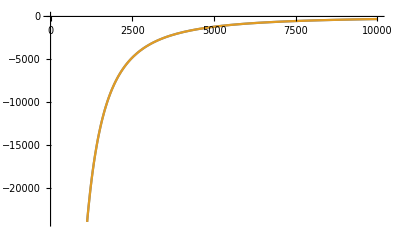

```mathematica
Plot[{pa[r],po[r]},{r,0,r0}]
```

```mathematica
po[5.]
```

-1.69978×10^9

Untuk ditulis di fortran

```mathematica
Clear["Global`*"];
FortranForm[p'[r]==((1+λ)^2 (l^4+l^2 r^2 (-2+λ)-r^4 (-1+λ^2)))/(4 G l^2 π r (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))+(2 r (1+λ) (-r^4 (-1+λ) (1+λ)^2+l^4 (1+2 λ)+l^2 r^2 (-2-2 λ+λ^2+λ^3)) p[r])/(l^2 (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))]
```

Derivative(1)(p)(r).eq.
     -  ((1 + λ)**2*(l**4 + l**2*r**2*(-2 + λ) - r**4*(-1 + λ**2)))/
     -    (4.*G*l**2*Pi*r*(l**2 - r**2*(1 + λ))*(l**2 + r**2*(-1 + λ**2))) + 
     -   (2*r*(1 + λ)*(-(r**4*(-1 + λ)*(1 + λ)**2) + l**4*(1 + 2*λ) + 
     -        l**2*r**2*(-2 - 2*λ + λ**2 + λ**3))*p(r))/
     -    (l**2*(l**2 - r**2*(1 + λ))*(l**2 + r**2*(-1 + λ**2)))

```mathematica
FortranForm[(5.4035243505523724 10^-2+(-3.0035243505523720*10^-2))*10^4]
```

240.

```mathematica
5.4035243505523724 10^2==-(-3.0035243505523720*10^2)+240.
```

True

```mathematica
Solve[-3.0035243505523720*10^-2 ==5.4035243505523724* 10^-2+x,x]
```

{{x→-0.0840705}}